# HitchHikers Guide to Computational Thinking With the Wolfram Language By, Jackreece Ejini

This is just another introduction to programming and computational thinking with the Wolfram Language. The Wolfram Language is the most sophisticated programming Language out there for doing all kinds of things programming. Despite its sophistication it is also one of the easiest programming language you can learn, my journey to becoming a computer programmer was a horrendous one because I did not know of the Wolfram Language. I know of many people that have abandoned thier dreams of becoming computer programmers because after foraying into the jungle of low level languages like C or “Object Oriented” languages like C++ and JAVA, they still did not know what programming was all about, they could follow through with the syntax of these langauges, that just requires having a good memory, but when it came to applying what they have learnt, expressing the solutions to real life problems computationally, they found it very had to make that abstract leap that is most essential to thinking about things computationally. The book AN ELEMENTARY INTRODUCTION TO THE WOLFRAM LANGUAGE, by STEPHEN WOLFRAM, is the best introduction to the WOLFRAM LANGUAGE and computational thinking I have ever come accross, and best of all the online version of this book is free! you can also get a hard copy for a fair price. This work is merely to supplement that but I strongly recommend that you read that to strengthen your foundations. This book is also necessary as a refresher that will strengthen the concepts you learnt in that book further. 

The WOLFRAM LANGUAGE is unique because you can do things that will be ridiculously difficult to do in order languages in a very short period of time, being a knowledge based language, most of the kinds of data you would have to obtain from other sources, most times at a great price, are already available for instant computation within the language itself, this is perfect for most beginers because obtaining high quality curated data is not usually an easy endeavour.

Although you can literally build piece of software completely with the WOLFRAM language alone, in the real world you might have to work at other software projects, sometimes because of the job you might happen to be involved in, I STRONGLY RECOMMEND THAT IF YOU HAVE NOT PROGRAMMMED A COMPUTER BEFORE YOU SHOULD PLEASE START YOUR JOURNEY WITH THE WOLFRAM LANGUAGE. I cannot over emphasize this point, it will save you many horrors, your learning rate is going to be near exponential. 

The WOLFRAM LANGUAGE provides what we call a NOTEBOOK, personally I call it an interactive exploration ground, you input code and you get results instantly, although some form on interactive programming is available in python, the WOLFRAM NOTEBOOK  environment is the most sophisticate programming education environment I have come across, from fancy visualization to the ability to tame the errors of beginning programmers. Another advantage to using the Wolfram Language is that because it is so high level, we focus more on the problem we want to solve and less on the specific details of the language. I usually call the Wolfram Language a disciplined kind of English Language because it is so clear and direct. The goal of any Wolfram Language programmer, like you are about to become is to reach a stage after a fair period of practice where you can start thinking directly in the Wolfram Language, this is what I call Wolfram Language Enlightenment! 

Without further ado, let us dive in to Computational thinking with the Wolfram Language.

## WHAT DOES A COMPUTER REALLY DO?

Basically:
1. Performs billions to trillions of Calculations per second!
2. Remembers the results of the calculations and sometimes display it!

What kinds of calculations can the computer perform
1. There are built-in calculations you can do directly with the Wolfram Language 
2. You can also define your own calculations.

Computers cannot do anything on their own! Only what you or someone else had tells them to do.

```mathematica
A basic computation
```

A basic computation

```mathematica
7 + 4
```

11

To compute anything and view your results in the Wolfram Language, you simply open a Notebook and type your computation at the beginning of the prompt in what we call a CELL, press SHIFT+ENTER and viola, your results appears instantly on the following line, this is basically what we do when we are computing in the wolfram language. Go ahead and do this with your Wolfram System, a free one is always available online at: WOLFRAM CLOUD

```mathematica
radius = 5;
areaOfCircle = Pi * radius^2
```

25 π

Suppose we want to calculate the AREA of a circle with radius 5, we can remember from school that the formula for the Area of a circle is πr^2, in the Wolfram language we assign 5 to the value of radius and enter the formula like we do on the second line. Note that I put a semi-colon after 5 above. This is to tell the Wolfram language that we do not want to see the result of the computation immediately. In the second line we now use radius in the computation and assign the output to another variable name areaOfCircle. 

What are variables, they are like names. We could have done the above computation like this using the formula directly:

```mathematica
Pi * 5^2
```

25 π

But assigned the value 5 to the variable name radius and then the result of our computation to the variable areaOfCircle. Most times when computing with the wolfram language we do not bother about naming everything just like some of you must have experienced in other programming languages. We could just go ahead and enter our computations and get the results.
The = sign is what we use to set radius to 5 and areaOfCircle to the result of the calculation. This is called and assignment. Another new thing is the * this is the multiplication sign in the Wolfram language. Another way to do multiplication would be to leave a space between two things we want to multiply

```mathematica
34 56
```

1904

The Wolfram language automatically displays the x multiplication sign when we input to things separated by a space. Another new thing we encounter is the upper caret sign ^ this is how we square things in the wolfram language. Above you can see that we are squaring the value of radius. There is a beautiful way to input the square of something, we type the thing like say radius followed by pressing CTRL + 6, then we get something like this radius^2, remember to press CTRL + SPACEBAR to return the cursor to its default location. You must we wandering were we got the Pi from. It is a built in symbol in the Wolfram Language. Unlike having to do something like pi = 3.14 like you would do in other languages, we simply type Pi because the Wolfram Language already knows what Pi is and we can use it directly in our computation. 
Unfortunately the result we get from our computation 25 π is not what we expected from a calculation of the area of a circle, this is because Pi is what we call a symbol in the Wolfram Langauge and the language can operate directly on symbolic variables. In the Wolfram language we can do things like this:

```mathematica
y = m x + c
```

c+m x

```mathematica
y
```

c+m x

```mathematica
boy
```

boy

```mathematica
girl
```

girl

These are referred to as symbols in the Wolfram Language, you can’t do this in many other languages because the language expect that you are trying to define a variable without a value and assumes that as an error. This is not a problem in the Wolfram Language. Now what do we do with our symbolic result 25 π ? In this case we can ask for a value

```mathematica
N[25 π]
```

78.5398

Now this looks like something we can relate to. That’s the area of the circle of radius 5, but 5 what? Lets say we want to compute for 5 centimeters, we simply say

```mathematica
radius1 = Quantity[5,"Centimeters"];
areaOfCircle1 = Pi*radius1^2;
answer = N[areaOfCircle1]
```

78.5398 cm^2

So what is N[ ], Quantity[ ]? These are built in functions in the Wolfram Language. A function is like a machine that does things for us, we just have to feed it some input, Later on we will learn how to build our kinds of functions that do stuff for us that we want to do but are not available in the Wolfram Language. When “calling” a function we start with its name, N or Quantity like in this example, put the beginning [ followed by the function “arguments” followed by a closing ] then our usual SHIFT + ENTER. The function then returns its results on the line following the input except we put a semi-colon ; after the call. N produces the Numerical equivalent of a its argument if one is available and Quantity converts some values into certain units. In this case we convert the value 5 to Centimeters. 

Although we can store represent something like the name of a person as a Symbol, it is usually better to store it as a STRING.

```mathematica
firstName = "Neo"
```

Neo

To create a string we start with an opening quote “ enter the string and follow it with a closing quote “ in this example, we assign the string Neo to the variable firstName.

```mathematica
surName = "Anderson"
```

Anderson

```mathematica
fullName = firstName <> surName
```

NeoAnderson

The less than greater than <> symbol is used to concatenate both the first and surnames together, we get a the fullName without spaces in the result. To add a space

```mathematica
fullName = firstName <> " " <> surName
```

Neo Anderson

You guessed right! we concatenate a whitespace character, gotten by merely starting the “ pressing space on your keyboard and followed with pressing “. 

Since this is a Hitch Hikers Guide, lets go through some of the kinds of functions that you will be using very regularly in the Wolfram Language, remember that a Function is merely a machine and with the right arguments, stuff it works with, it will produce some output.

# Quick diving ...

SUM OF THE FIRST 10 NUMBERS

```mathematica
Range[10] (* The first 10 numbers *)
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Total[Range[10]] (* Sum of the first 10 numbers *)
```

55

The stuff after the computation (* Sum of the first 10 numbers *) is referred to as a comment in the Wolfram Language. It does not compute to anything but merely serve as a signpost for the reader of your code to get an explanation of what your code is doing. As you can see in this example we are Nesting one function within another. The inner function is called and the results are passed to the outermost function, we did not capture the output in a variable, this is how most sophisticated WL (Wolfram Language) code is written.

```mathematica
Reverse[Range[10]]
```

{10,9,8,7,6,5,4,3,2,1}

The name of the function simply tells us what the function is doing.

```mathematica
Range[2,20,2] (* Even numbers *)
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
Range[2,20,2]*2 (* Multiply them by 2 *)
```

{4,8,12,16,20,24,28,32,36,40}

The 2 is used to multiply each even number in the list we got. We could perform other operations on a list of values

```mathematica
Range[2,20,2]^2 (* Square each by 2 *)
```

{4,16,36,64,100,144,196,256,324,400}

Or use the nicely formatted version of powering

```mathematica
Range[2,20,2]^6(* To the sixth power *)
```

{64,4096,46656,262144,1000000,2985984,7529536,16777216,34012224,64000000}

We can use any interval

```mathematica
Range[1, 100, 3]
```

{1,4,7,10,13,16,19,22,25,28,31,34,37,40,43,46,49,52,55,58,61,64,67,70,73,76,79,82,85,88,91,94,97,100}

```mathematica
Range[1, 100, 3^2]
```

{1,10,19,28,37,46,55,64,73,82,91,100}

```mathematica
Table[If[Mod[n,2]==0,n,Nothing],{n,1,10,1}] (* Another method of generating even numbers *)
```

{2,4,6,8,10}

More Complicated than our Range method above. We use an If function to make decisions. Its form is If[condition, true, false]. If condition evaluates to true the first result for true is “Evaluated” and returned out of the function, if its false the last statement is evaluated, a symbolic Nothing in this case. The Mod function performs the modulus of its arguments. When we divide one number by another we get the quotient and a remainder, if a number divides perfectly without a remainder the modulus is 0. This is not a perfectly accurately description and there is a whole field of discrete mathematics that deals with this stuff, but for our purposes in the above program, we do a Mod of a number n with 2, that result will be equal to 0 if that number divides perfectly with 2, which is a basic test for Even numbers. 
Table is a very powerful iteration function, we use it more often that For statement in WL. Lets drill through it to understand a little better.

```mathematica
Table[n, {n,1,10,1}] (* simple table that returns numbers from 1 to 10 *)
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[10] (* Range equivalent *)
```

{1,2,3,4,5,6,7,8,9,10}

n is called the iterator variable. We start from 1 to 10 in steps of one.

```mathematica
Table[n, {n, 2, 10,1}] (* We can start some other place *)
```

{2,3,4,5,6,7,8,9,10}

```mathematica
Table[n,{n,2,10,2}] (* Our Even numbers *)
```

{2,4,6,8,10}

```mathematica
Table[If[EvenQ[n],n,Nothing],{n,1,10,1}] (* We use EvenQ function in this case to check for evenness *)
```

{2,4,6,8,10}

```mathematica
Table[n^2, {n,1,10,1}] (* First 10 Squares *)
```

{1,4,9,16,25,36,49,64,81,100}

n is not special we can name the iteration variable anything

```mathematica
Table[value, {value,5,20,3}]
```

{5,8,11,14,17,20}

It’s always a good idea to name your iteration variables according to its purpose.

## Dancing with Strings...

```mathematica
"A simple statement"
```

A simple statement

```mathematica
StringLength[%] (* The modulus operator is used to remember the last output *)
```

18

StringLength just gets the length of a string

```mathematica
StringLength["I love the Wolfram Language"]
```

27

```mathematica
statement = "I love the Wolfram Language"
```

I love the Wolfram Language

```mathematica
StringPart[statement, 3] (* Lets get l in love *)
```

l

```mathematica
StringPosition[statement,"W"] (* The index position of "W" in the string *)
```

{{12,12}}

```mathematica
StringPosition[statement,"m"] (* The index position of "m" in the string *)
```

{{18,18}}

```mathematica
StringTake[statement,12;;18] (* We use the indices to extract Wolfram from the string *)
```

Wolfram

Another way, WL has many ways to solve the same problem.

```mathematica
StringPart[statement,12;;18]
```

{W,o,l,f,r,a,m}

Use CTRL + L to get the previous computation

```mathematica
StringJoin[StringPart[statement,12;;18] ]
```

Wolfram

When you know enough of WL you will find other ways to do this... Lets explore one more

```mathematica
Characters["Wolfram"]
```

{W,o,l,f,r,a,m}

```mathematica
StringJoin[Characters["Wolfram"]]
```

Wolfram

```mathematica
Characters["Wolfram Language is awesome"]
```

{W,o,l,f,r,a,m, ,L,a,n,g,u,a,g,e, ,i,s, ,a,w,e,s,o,m,e}

```mathematica
Position[Characters["Wolfram Language is awesome"],"L"]
```

{{9}}

```mathematica
Position[Characters["Wolfram Language is awesome"],"e"]
```

{{16},{23},{27}}

From eyeballing the text and the indices we can see that the first time we see “e” is at the end of language.

```mathematica
Take[Characters["Wolfram Language is awesome"],9;;16]
```

{L,a,n,g,u,a,g,e}

```mathematica
StringJoin[Take[Characters["Wolfram Language is awesome"],9;;16]]
```

Language

What is 9 ;; 16 ? or index ;; index? It’s called taking a part.

```mathematica
Part[Characters["Wolfram Language is awesome"],9;;16]
```

{L,a,n,g,u,a,g,e}

The Part function uses indices to extract parts of an expression.

```mathematica
StringTake["Wolfram Language is awesome", 9;;16] (* Another nice way to extract parts of a String *)
```

Language

## Word of Advice

When learning programming, you start by learning the syntax. After learning the syntax you next step is digging through the documentation. Like I always say KEEP YOUR DOCUMENTATION UNDER YOUR PILLOW. When you go through the WL documentation you will see all these functions in great detail, plus it’s well written.

```mathematica
{4,5, 6 ,7, 1, 3}
```

{4,5,6,7,1,3}

We have been using something with and opening curly brace { some numbers separated by commas followed by a closing curly brace }. This structure is known as a List in WL. It is the most fundamental kind of structure you will be dealing with most of times. Most functions return Lists as their result and Many operate directly on List.

```mathematica
{"a","b","c"} (* We can put characters *)
```

{a,b,c}

```mathematica
{"eggs", "bananas","oranges"} (* And some strings *)
```

{eggs,bananas,oranges}

The List is a container we use it to hold stuff, it’s implemented very efficiently in WL Most of the time in your computations you will be dealing with Lists.

```mathematica
{2,"houses", 4, "cars", 5,"boats"} (* You can mix stuff up *)
```

{2,houses,4,cars,5,boats}

```mathematica
{{2,"houses"},{4,"cars"},{5,"boats"}} (* Or use a Nested List to create some data Structure *)
```

{{2,houses},{4,cars},{5,boats}}

```mathematica
{{2,"houses"},{4,"cars"},{5,"boats"}}[[2]] (* Get the second item using an index *)
```

{4,cars}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[10][[3]] (* The 3rd item *)
```

3

```mathematica
Part[Range[10],3] (* With Part function *)
```

3

```mathematica
Range[10][[2;;6]] (* Gets the 2nd to the 6th item *)
```

{2,3,4,5,6}

```mathematica
Range[10][[-1]] (* Last Item *)
```

10

```mathematica
Last[Range[10]] (* Last function for last item *)
```

10

```mathematica
First[Range[10]]
```

1

```mathematica
Rest[Range[10]] (* Without the first *)
```

{2,3,4,5,6,7,8,9,10}

```mathematica
Most[Range[10]] (* Without the Last *)
```

{1,2,3,4,5,6,7,8,9}

```mathematica
{{2,"houses"},{4,"cars"},{5,"boats"}}[[2]]
```

{4,cars}

Lets go deeper

```mathematica
{{2,"houses"},{4,"cars"},{5,"boats"}}[[2,1]]
```

4

```mathematica
{{2,"houses"},{4,"cars"},{5,"boats"}}[[2,2]]
```

cars

```mathematica
{{2,"houses"},{4,"cars"},{5,"boats"}}[[2]][[1]] (* Another way *)
```

4

```mathematica
Part[{{2,"houses"},{4,"cars"},{5,"boats"}},2,1] (* Neater using Part *)
```

4

```mathematica
Part[{{2,"houses"},{4,"cars"},{5,"boats"}},2,2]
```

cars

```mathematica
Part[{{2,"houses"},{4,"cars"},{5,"boats"}},3]
```

{5,boats}

```mathematica
l1 = {1,2,3,4,5};
l2 = {56,3,4,67,7};
```

```mathematica
Join[l1,l2] (* The built-in function Join is used to joint lists together *)
```

{1,2,3,4,5,56,3,4,67,7}

```mathematica
l3 = {"a","b","c","d"};
```

```mathematica
Join[l1,l2,l3] (* We can Join a number of lists *)
```

{1,2,3,4,5,56,3,4,67,7,a,b,c,d}

```mathematica
Prepend[l1,90] (* Add 90 to the front of l1 *)
```

{90,1,2,3,4,5}

```mathematica
Append[l1,123] (* Add 123 to the end *)
```

{1,2,3,4,5,123}

```mathematica
ReplacePart[l1,1000,4] (* Replace the 4th part of the list with 1000 *)
```

{1,2,3,1000,5}

```mathematica
l1 (* The original list remains *)
```

{1,2,3,4,5}

```mathematica
ReplacePart[l2,zzz,3] (* Replace the 3 part of l2 with zzz *)
```

{56,3,zzz,67,7}

```mathematica
Delete[l1,3] (* Remove the item at part 3 *)
```

{1,2,4,5}

```mathematica
longlist = Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Delete[longlist,{{5},{10},{15}}] (* Remove items at various locations *)
```

{1,2,3,4,6,7,8,9,11,12,13,14,16,17,18,19,20}

```mathematica
RandomInteger[10] (* Random Integer between 1 and 10 *)
```

7

A bunch of them in a List

```mathematica
RandomInteger[10,10] (* 10 numbers between 1 and 10 *)
```

{0,10,9,10,2,3,4,8,0,9}

```mathematica
randInts = % (* save it *)
```

{0,10,9,10,2,3,4,8,0,9}

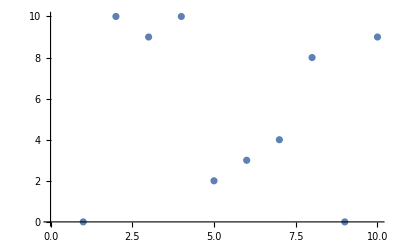

```mathematica
ListPlot[randInts]
```

I prefer seeing a line

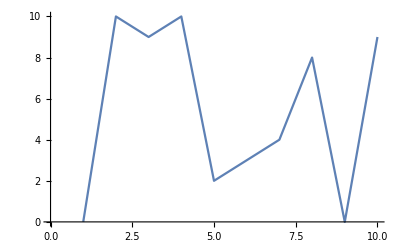

```mathematica
ListLinePlot[randInts]
```

Some deeper structure

```mathematica
RandomInteger[10,{3,6}] (* 3 Lists of 6 items each *)
```

{{0,2,1,6,5,5},{5,6,4,1,6,9},{3,3,2,3,5,0}}

```mathematica
RandomInteger[10,{6,3}] (* 6 Lists of 3 items each *)
```

{{2,5,4},{4,10,10},{7,4,10},{0,1,7},{7,3,6},{5,2,4}}

Even deeper, depth is measured by Levels of Nesting

```mathematica
RandomInteger[100,{13,6,5,3}]
```

{{{{50,71,94},{58,43,30},{71,17,60},{53,76,85},{3,72,30}},{{86,73,98},{52,82,35},{64,66,28},{52,15,0},{51,54,39}},{{37,20,63},{89,4,32},{83,74,20},{20,6,13},{31,61,32}},{{12,51,59},{3,74,72},{85,85,97},{50,76,100},{57,92,68}},{{77,49,7},{30,38,92},{67,45,37},{51,95,70},{70,62,31}},{{88,1,75},{3,83,9},{11,42,66},{62,6,16},{94,89,87}}},{{{19,42,45},{61,91,62},{37,89,71},{11,30,8},{27,17,1}},{{85,18,34},{61,7,14},{99,42,10},{15,88,29},{90,26,55}},{{27,48,19},{90,65,41},{59,62,91},{57,100,91},{25,99,0}},{{78,16,30},{77,51,13},{92,73,26},{40,88,67},{93,67,87}},{{44,26,17},{15,34,51},{51,35,6},{43,15,81},{59,4,63}},{{44,5,44},{15,79,78},{75,77,67},{53,50,50},{87,97,72}}},{{{13,63,83},{99,48,83},{25,17,29},{62,37,80},{7,72,71}},{{97,90,15},{26,44,81},{67,80,83},{18,28,43},{65,1,26}},{{13,96,21},{32,3,76},{27,34,50},{48,63,25},{73,49,88}},{{88,71,56},{95,5,64},{62,94,84},{52,59,60},{83,7,33}},{{5,63,21},{17,10,46},{84,64,22},{49,49,63},{37,63,20}},{{15,8,9},{55,41,10},{92,2,54},{56,38,3},{97,43,59}}},{{{29,14,24},{50,43,79},{48,32,14},{61,6,85},{63,50,15}},{{97,88,9},{34,1,30},{66,27,4},{81,4,92},{97,5,13}},{{69,66,53},{97,7,9},{8,55,64},{58,3,10},{77,28,78}},{{99,54,42},{45,19,48},{24,64,88},{27,71,39},{57,12,95}},{{30,30,30},{37,18,59},{82,18,37},{61,27,51},{64,35,80}},{{65,11,95},{10,2,2},{86,13,53},{38,43,1},{77,64,45}}},{{{41,9,52},{31,72,50},{89,10,52},{88,14,15},{57,57,21}},{{21,48,81},{38,46,96},{87,21,99},{4,42,81},{27,59,3}},{{28,11,40},{65,40,55},{98,57,97},{50,46,84},{72,38,54}},{{30,10,86},{40,84,63},{88,79,84},{84,63,60},{32,41,38}},{{10,21,51},{86,45,2},{2,88,11},{8,33,44},{40,91,7}},{{56,7,47},{46,79,19},{89,50,58},{64,82,0},{45,3,4}}},{{{9,76,66},{14,86,96},{24,28,76},{67,100,87},{24,62,55}},{{72,76,84},{37,96,92},{21,93,35},{91,91,66},{5,6,77}},{{95,53,30},{72,39,71},{99,69,65},{71,16,39},{4,73,39}},{{6,8,76},{8,63,69},{28,84,90},{72,84,23},{82,2,1}},{{38,92,95},{32,60,65},{23,71,61},{88,8,71},{28,7,66}},{{94,77,78},{7,35,44},{95,69,26},{55,92,23},{24,97,92}}},{{{22,63,93},{27,4,80},{26,21,2},{66,92,47},{77,50,40}},{{71,48,32},{76,27,49},{45,10,90},{62,29,16},{21,48,67}},{{96,25,74},{76,61,48},{95,74,38},{11,65,87},{41,46,65}},{{45,62,40},{90,30,68},{49,97,80},{7,97,64},{27,43,46}},{{41,41,28},{80,17,39},{24,77,70},{92,53,68},{39,18,19}},{{77,17,2},{93,4,52},{24,52,79},{25,29,76},{11,1,16}}},{{{37,21,57},{34,94,74},{81,75,9},{77,41,62},{40,27,29}},{{5,0,28},{27,29,100},{67,42,84},{56,48,17},{79,67,77}},{{97,61,4},{51,79,20},{100,79,81},{87,84,33},{51,62,18}},{{87,98,17},{76,51,2},{62,58,24},{92,84,6},{15,9,50}},{{24,69,36},{86,40,72},{96,25,80},{63,56,44},{35,43,1}},{{26,87,33},{36,21,71},{39,78,17},{66,1,31},{85,92,17}}},{{{29,62,19},{57,61,32},{75,42,53},{75,44,73},{59,25,17}},{{45,13,65},{80,61,9},{68,93,34},{46,57,44},{60,35,21}},{{20,91,13},{52,99,41},{17,34,9},{99,89,12},{95,51,23}},{{23,75,68},{32,54,63},{6,16,13},{31,59,61},{29,6,6}},{{56,35,72},{8,51,88},{24,30,16},{36,77,56},{39,84,50}},{{41,78,59},{44,57,39},{24,49,45},{97,1,82},{52,42,80}}},{{{64,80,13},{53,51,87},{48,91,27},{38,61,26},{15,84,92}},{{26,31,32},{77,68,35},{40,78,12},{56,31,94},{7,42,93}},{{4,72,90},{19,33,31},{89,45,51},{84,95,97},{71,31,16}},{{87,26,56},{23,29,38},{60,30,73},{78,67,78},{58,63,13}},{{13,62,15},{65,87,59},{80,30,69},{89,98,72},{56,51,86}},{{73,73,34},{90,12,15},{47,25,54},{36,40,80},{97,1,22}}},{{{28,23,51},{83,31,29},{90,69,81},{84,56,19},{88,29,36}},{{73,6,19},{65,39,69},{6,81,41},{97,12,27},{46,96,27}},{{96,20,76},{62,1,72},{33,58,3},{82,29,85},{15,75,76}},{{63,84,61},{93,33,58},{80,70,26},{40,64,34},{69,42,52}},{{88,57,28},{52,48,95},{28,5,68},{85,90,38},{97,38,67}},{{82,71,40},{45,60,94},{79,18,33},{87,18,27},{89,2,30}}},{{{90,9,72},{21,22,51},{8,20,90},{95,73,79},{81,6,97}},{{54,76,21},{93,3,30},{10,1,14},{75,36,6},{9,26,3}},{{96,17,43},{74,77,15},{90,56,93},{6,52,62},{36,52,43}},{{73,35,35},{76,23,48},{76,15,57},{70,70,70},{25,95,43}},{{59,56,73},{66,55,52},{8,17,55},{90,0,42},{66,1,20}},{{50,83,86},{75,83,56},{37,30,35},{9,100,39},{62,78,100}}},{{{90,21,38},{22,81,74},{94,97,38},{16,80,98},{44,11,55}},{{9,63,96},{1,72,7},{65,38,53},{3,38,37},{18,86,90}},{{97,55,44},{13,33,2},{24,4,10},{81,77,100},{46,79,34}},{{92,60,18},{29,70,67},{89,69,3},{3,39,42},{83,19,19}},{{63,62,9},{97,89,97},{70,95,69},{91,40,9},{28,95,22}},{{92,5,75},{97,16,69},{39,22,5},{77,98,32},{49,49,26}}}}

```mathematica
Short[RandomInteger[100,{13,6,5,3}]] (* Short to show a surmarised version of some Long list *)
```

{«1»}

```mathematica
Dimensions[RandomInteger[100,{13,6,5,3}]](* Dimensions gives us the Dimensionality of some Structure so we can know how many levels of nesting we're dealing with *)
```

{13,6,5,3}

```mathematica
RandomInteger[{20,40},14] (* Random numbers between 20 and 40 *)
```

{34,31,26,21,33,37,22,35,29,34,30,20,34,32}

```mathematica
Length[RandomInteger[100,{13,6,5,3}]] (* Gives you the length of the outermost layer of the nested list *)
```

13

If we have a one dimensional list

```mathematica
RandomInteger[100,100]
```

{36,18,14,5,16,89,25,21,49,28,43,11,56,61,64,28,11,38,4,6,7,86,34,9,49,83,86,70,10,58,30,49,18,51,38,30,99,22,40,71,63,78,78,8,40,36,34,7,67,62,70,0,41,82,20,90,87,82,78,82,6,36,89,4,29,2,84,83,5,42,68,26,26,1,43,34,29,81,88,64,18,17,57,13,25,64,35,9,16,58,39,42,13,58,92,95,5,85,58,83}

The best way to gain some idea about these numbers is to plot them, personally I prefer using a line plot

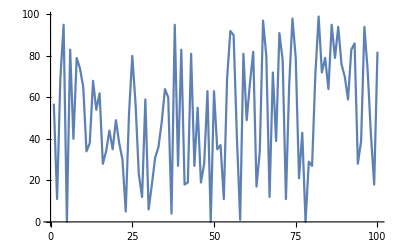

```mathematica
ListLinePlot[RandomInteger[100,100]]
```

A better choice of graphing in this case could be a Histogram

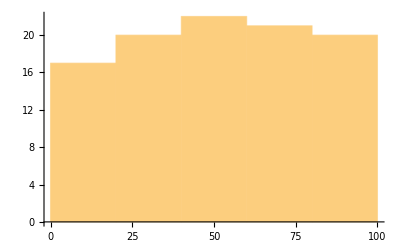

```mathematica
Histogram[RandomInteger[100,100]]
```

Sometimes we have two dimensional data

```mathematica
RandomReal[1,{100,100}]
```

{{0.366633,0.880055,0.832618,94,0.88174,0.0885057,0.772699},98,{1}}
 |  |  |  |

```mathematica
Length[Dimensions[RandomReal[1,{100,100}]]] (* Getting the Dimensionality of data *)
```

2

To view such data we use some tools like

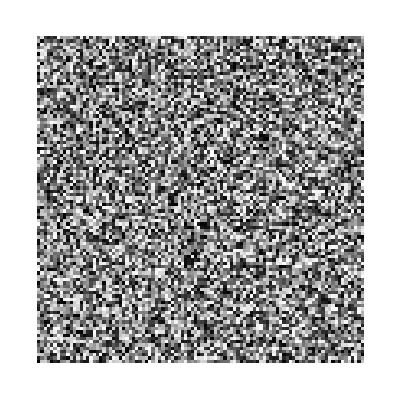

```mathematica
ArrayPlot[RandomReal[1,{100,100}]]
```

The result is a random image

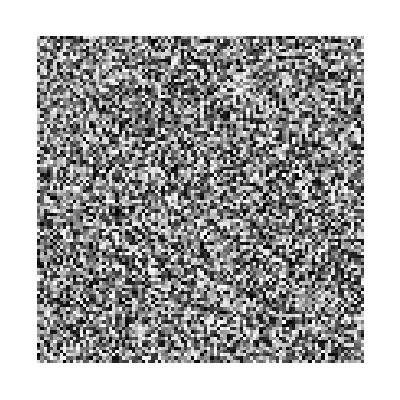

```mathematica
ArrayPlot[RandomReal[1,{100,100}], ImageSize->Tiny]
```

The ImageSize -> Tiny directive is an option. Most built in functions have options that customize the operations of a function. In this case we specify that we want a tinier version of the Image above.
Remember that anytime we call the RandomInteger or RandomReal function a fresh set of random numbers is generated every time. To save what we have generated we only need to create a variable name.

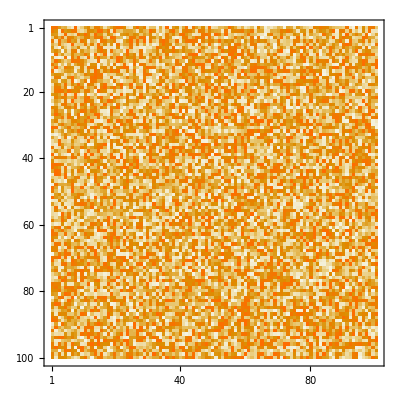

```mathematica
MatrixPlot[RandomReal[1,{100,100}]]
```

A much colorful visualization.

```mathematica
RandomSample[Range[100],20] (* Obtain a random sample of 20 items from 100 *)
```

{13,19,37,78,56,58,8,81,85,29,77,76,80,31,9,27,52,89,96,51}

We can even visualize things in 3D.

```mathematica
ListPlot3D[RandomReal[1,{10,10}]] (* A 2D surface in 3D space *)
```

-Graphics3D-

```mathematica
ListPointPlot3D[RandomReal[1,{10,10,3}]] (* A bunch of points in 3D space *)
```

-Graphics3D-

There are many types of visualization available in the Wolfram Language, going through the documentation is a nice way to see whats available.

```mathematica
RandomSample[Range[100]] (* Another way to randomize a list things *)
```

{94,24,77,16,97,23,48,65,1,11,31,76,27,63,21,57,71,83,61,12,53,14,56,60,79,6,7,64,92,96,39,69,73,41,28,18,20,81,89,4,19,40,33,52,42,17,25,84,35,46,22,13,62,38,66,2,26,67,80,54,9,99,85,8,49,29,55,44,32,10,36,93,70,3,82,37,87,59,90,68,91,95,34,78,43,5,30,15,86,51,50,45,88,75,98,47,74,58,72,100}

if you have forgotten what Range does, you could literally take out the code for Range[100] and run it independently, after which you will see clearly what RandomSample does. Breaking up complicated pieces of code in such a manner to understand the individual pieces is a skill that you will need when reading code in the wild.

```mathematica
RandomChoice[{"bread","butter","cheese","milk"}] (* Making a random choice *)
```

butter

```mathematica
RandomChoice[{"bread","butter","cheese","milk"}] (* Making a random choice *)
```

cheese

We mostly get some random item every time we run RandomChoice on a list of items.

## Defining our own FUNCTIONS

So far we have used the built-in WL functions to do most of our computation, for most well defined tasks there are built-in WL functions that perform them very efficiently but for some arbitrary task we might want to perform, there may be no built-in functions that do it so we end up having to define our own functions. Before you decide to write your functions, it might be wise to first of all check the documentation as what you are trying to do might already exist, to avoid reinventing the wheel.

```mathematica
x = RandomInteger[10]
```

6

Above we assign x to a RandomInteger between 0 and 10 using the single equals sign, this what you might have seen in many other programming languages. But in WL we have another type of assignment

```mathematica
y := RandomInteger[10]
```

The first one is called Immediate assignment while the second one is called delayed assignment. In the first one a RandomInteger is generated an Immediately assigned to a variable, this is like saving that number.

```mathematica
x
```

6

```mathematica
x
```

6

No matter how many times we ask for the value of x by executing it with our usual SHIFT + ENTER, we get the value that was generated the very first time.

```mathematica
y
```

9

```mathematica
y
```

2

```mathematica
y
```

1

In the second case when we first did a delayed assignment of y to a RandomInteger, we essentially put the computation of RandomInteger on hold. The delayed assignment essentially says do not compute until I explicitly request. So whenever we request a value for y we get a new value because we are re-evaluating RandomInteger each time.

```mathematica
isEven[n_]:=If[Mod[n,2]==0,True,False]
```

```mathematica
isEven[2]
```

True

```mathematica
isEven[3]
```

False

We define a function named isEven which receives a number and checks if its even, and returns True or False depending. The parameter named n is assigned whatever we pass into this function when we call it, which is further passed to the body of the function where further computation takes place, in this case a single If function.
Why do we put a single _ after the n? The underscore is called a pattern expression in WL. A pattern is an expression which matches another expression. In this case we are saying we want to match any single expression available in WL. the n is just a name for this pattern which we use to remember the pattern inside the body of the function expression.

```mathematica
isOdd[number_]:=If[Not[Mod[number,2]==0], True, False]
```

```mathematica
isOdd[2]
```

False

```mathematica
isOdd[3]
```

True

As we can see we are not limited to single letters like n for our parameter names, we can name our parameters with names like number_ to give the user of the function an idea of the parameter type.

```mathematica
isEven[t]
```

If[Mod[t,2]==0,True,False]

We see that is used the symbol t inside the function and since I did not define the function to handle arbitrary symbols, the call fails and returns the body of the function. A nice way to tell the user about what kind of arguments a function takes is to include the head type of the parameter after the underscore

```mathematica
isOdd[number_Integer]:=If[Not[Mod[number,2]==0], True, False]
```

We can also put conditions on the arguments to functions

```mathematica
factorial1[n_/;n>0]:=n! (* Find the factorial of only positive integers *)
```

The condition the n must be greater than 0 is given after the slash-colon /;

```mathematica
factorial1[6]
```

720

```mathematica
factorial1[-5] (* doesn't work for negative numbers *)
```

factorial1[-5]

We can still define functions with default values

```mathematica
fibonacci[0] = 0; fibonacci[1]=1; fibonacci[n_:8]:=fibonacci[n]=fibonacci[n-1]+fibonacci[n-2]
```

We can call this function without providing arguments, not that it is necessary I just wanted a demonstration of this facility.

```mathematica
fibonacci[]
```

21

```mathematica
fibonacci[10]
```

55

But as usual there is a better way to do this things with built-in functions, always use the  documentation to check for a solution to what you want to do, you might just find it. It is a convention to use lowercase letters for function names that we define ourselves

```mathematica
Fibonacci[10]
```

55

## Heads!

Expression in the Wolfram Language has a head and we can get the name of the head of an expression using Head.

```mathematica
Head[x] (* remember the variable x we defined sometime ago *)
```

Integer

```mathematica
Head[t] (* has not been assigned anything yet and so its just a symbol *)
```

Symbol

```mathematica
Head[{}] (* The curly brace has head list *)
```

List

```mathematica
Head["Apples"]
```

String

Internally the Wolfram Language converts the curly brace {} into something with head List.

```mathematica
FullForm[{1,2,3}]
```

List[1,2,3]

Sometimes we want to define a local constant inside a function.

```mathematica
byThousand[value_]:=With[{multiplier = 1000}, value * multiplier]
```

```mathematica
byThousand[10]
```

10000

Note that With is just another built-in function and can be used on its own without being wrapped inside a function.

```mathematica
gcd[m0_,n0_]:=
Module[{m=m0,n=n0},(* We capture the arguments and assign them to variables m and n *)
While[n≠0,{m,n}={n,Mod[m,n]}]; (* In this line we do multiple simultaneous assignment *)
m
]
```

```mathematica
gcd[18,12]
```

6

In this case we use Module to define local variables inside a function gcd function, gcd stands for greatest common divisor. We did not use With because during the computation we change the values of m and n, that is why we need a variable rather than a constant. As you gain more experience with WL you will know when its appropriate to use With or Module.

## Pure functions

```mathematica
#+2&
```

#1+2&

Above is the definition of a simple pure function. Pure functions are sometimes called anonymous functions because we do not need a name when we are defining them. The # is called a slot variable, this is the variable that will be latter assigned a value when we call the function. the & indicates the end of the function. When we evaluate a pure function all that happens is that it just returns the entire definition on the output line with the slot variable being given a number.

```mathematica
(#1 + #2)/10&
```

(#1+#2)/10&

We can also have multiple arguments or parameters to a pure function, each parameter being replaced by the appropriate slot number.

## Calling functions

```mathematica
# + 2&[10] (* Supply a single argument to a pure function *)
```

12

```mathematica
(#1 * #2)/#3&[2,3,5] (* Multiple arguments *)
```

6/5

```mathematica
N[(#1 * #2)/#3&[2,3,5]] (* Call N the regular way *)
```

1.2

```mathematica
32234 / 45//N (* Double forward slash calls a function as an afterthought *)
```

716.311

```mathematica
Sqrt[7]
```

√7

```mathematica
N@Sqrt[7] (* Another way to call the N funtion *)
```

2.64575

## Recursion

It is a programming technique where a function calls itself. There are certain things to keep in mind when designing a recursive solution to a problem in programming. 
1. You must have 1 or more base cases so as to prevent infinite recursion.
2. Reduce the problem to simpler versions of the same problem.

Recursive multiplication example

```mathematica
multiply[a_,1]:=a; (* Base case *)
multiply[a_,b_]:= a+mult[a,b-1]
```

```mathematica
multiply[6,1] (* Test base case *)
```

6

```mathematica
multiply[9,7] (* Test main recursion *)
```

9+mult[9,6]

There is a much faster way to multiply in WL using the built-in Times function, the above program is only to show the concept of recursion

```mathematica
Times[9,7]
```

63

Find the FACTORIAL recursively. The definition of n! = n *(n-1) * (n-2) * (n-3) * ... * 1

```mathematica
factorial[1] = 1 ;(* Base case *)
factorial[n_]:=factorial[n]=n factorial[n-1] (* Recursive solution with factorial[n] spliced in to speed up computation, its a technique called memoization *)
```

```mathematica
factorial[10]
```

3628800

```mathematica
10! (* Using the more optimal built-in *)
```

3628800

## Pairing things

If we are given lists of items that are related in some way like a list of student names and associated scores:

```mathematica
names = {"Vestal","Denis","William","Joe"};
scores ={"A+","B","B","C"};
```

With each name in the names List associated with a corresponding score in the scores list. For example “Vestal” had an “A+“, because the name and the score are in the same position in both lists.
One way of pairing these lists is by Transposing them:

```mathematica
Transpose[{names,scores}]
```

{{Vestal,A+},{Denis,B},{William,B},{Joe,C}}

We can query this mini data structure using the usual indexing operations

```mathematica
Transpose[{names,scores}][[2]] (* Get the value for Denis *)
```

{Denis,B}

```mathematica
Transpose[{names,scores}][[4,2]] (* Get Joe's Score *)
```

C

There is a better way to handle these kinds of key -> value pairs in WL, its called associations.

```mathematica
grades = <|"Vestal"->"A+","Denis"->"B","William"->"B","Joe"->"C"|>
```

<|Vestal→A+,Denis→B,William→B,Joe→C|>

We type a “less than” < followed by a vertical bar | to start the association. We separate the key value pairs with a  dash - followed by a greater than > on the keyboard. This is how we create the rule notation -> which we will be see a lot later. The names are they Keys while the scores are the Values.

```mathematica
grades["Vestal"] (* Get Vestal's grade *)
```

A+

```mathematica
grades["Felix"] (* If we try to get a missing key we get a Missing[] *)
```

Missing[KeyAbsent,Felix]

```mathematica
grades["Felix"] = "A" (* Add a grade for Felix *)
```

A

```mathematica
grades
```

<|Vestal→A+,Denis→B,William→B,Joe→C,Felix→A|>

```mathematica
KeyDrop[grades,"William"] (* Delete a key *)
```

<|Vestal→A+,Denis→B,Joe→C,Felix→A|>

```mathematica
Keys[grades] (* Get the Keys *)
```

{Vestal,Denis,William,Joe,Felix}

```mathematica
Values[grades] (* Get the Values *)
```

{A+,B,B,C,A}

## Searching for stuff

In many other programming languages you might be required to implement your own search algorithms, but because WL has an enormous stack of extremely efficient algorithms for doing most things you will want to do there is no need to implement these algorithms yourself, you can free yourself to solve higher level computational problems rather than trying to optimize some algorithms for which far faster implementations have been done by experts. Like they say lets not re-invent the wheel. Many purist will argue that teaching these “fundamental” methods are important but in my view this misses the point of using a very high level knowledge based language like WL, there are more things in the life to bother about. If you are still interested in that kind of stuff you will also find implementing your version in WL very efficient.

```mathematica
Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Let us select all the even items from this list

```mathematica
Select[Range[20],EvenQ] (* Select items from a list for which a particular function, in this case EvenQ returns true *)
```

{2,4,6,8,10,12,14,16,18,20}

We can even build our own even function using a pure function

```mathematica
Select[Range[20],Mod[#,2]==0&] (* Select items from a list for which a particular pure function returns true # here represents each element from the list *)
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
someRandomInts =RandomInteger[10,10]
```

{1,0,5,10,4,1,6,8,0,1}

```mathematica
Select[someRandomInts,# >3&] (* all greater than 3 *)
```

{5,10,4,6,8}

You might see the operator form of select used sometimes

```mathematica
Select[OddQ][Range[10]]
```

{1,3,5,7,9}

```mathematica
Table[{n,If[EvenQ[n],even,odd]},{n,1,10}]
```

{{1,odd},{2,even},{3,odd},{4,even},{5,odd},{6,even},{7,odd},{8,even},{9,odd},{10,even}}

```mathematica
Select[Table[{n,If[EvenQ[n],even,odd]},{n,1,10}],MemberQ[#,odd]&] (* Use MemberQ to Select sublists that contain the odd symbol *)
```

{{1,odd},{3,odd},{5,odd},{7,odd},{9,odd}}

One goal I have in this book is to gradually bring the user to understand greater levels of complexity within code, the kind you will meet in the real world. I am trying as much as possible to automatically generate most of the data you see because real world code will require that you hold certain data structures mentally and observe operations being done on them. WL is a very compact language enabling you to say so much with so little and generate a lot of what you want to deal with automatically, so it is imperative that you start understanding nested pieces of code.
So rather than create a list manually like {1,2,3,4,5}, I will do Range[5]

More complex conditions

```mathematica
Select[Range[100], Mod[#,3] == 0 && Mod[#, 5] ==0&] (* Select numbers up to 100 that are divisible by both 3 and 5. The && is a logical AND *)
```

{15,30,45,60,75,90}

## Patterns

We use patterns in WL to search for stuff and possibly apply some kind of transformation to them.

```mathematica
Range[10]/.num_->num^2 (* using a named pattern to search a list and square every single item *)
```

{1,4,9,16,25,36,49,64,81,100}

The main pattern here is the underscore _, it matches single anything. It is preceded by a name num so that we use num in the transformation on the other side of the Rule -> symbol.
double underscore __ matches 1 one or more things while triple underscore matches zero or more things, we will see these patterns used in programs we will encounter.

```mathematica
Join[Range[3],Table[i^n,{n,1,3}],{j^3}]
```

{1,2,3,i,i^2,i^3,j^3}

```mathematica
Join[Range[3],Table[i^n,{n,1,3}],{j^3}]/.(i|i^_) -> q  (* This rule says turn any i or i to the power anything to q *)
```

{1,2,3,q,q,q,j^3}

The pattern language available in WL is more elegant than regular expressions found in other languages.

```mathematica
Join[RandomInteger[10,5],Characters["Wolfram"]]
```

{5,4,7,10,4,W,o,l,f,r,a,m}

```mathematica
wordsNnumbers =RandomSample[Join[RandomInteger[10,5],Characters["Wolfram"]]]
```

{l,7,3,W,o,2,a,r,m,f,5,4}

```mathematica
Cases[wordsNnumbers,_Integer] (* Find all integers *)
```

{7,3,2,5,4}

```mathematica
Cases[wordsNnumbers,Except[_Integer]] (* Find all non-integers *)
```

{l,W,o,a,r,m,f}

```mathematica
pairsNtriples = RandomSample[Join[RandomInteger[10,{3,2}],RandomInteger[5,{3,3}]]]
```

{{3,10},{0,0,2},{5,1,4},{5,1,5},{4,9},{10,6}}

```mathematica
Cases[pairsNtriples,{_,_}] (* Find all pairs *)
```

{{3,10},{4,9},{10,6}}

```mathematica
Cases[pairsNtriples,{_,_,_}] (* Find all triples *)
```

{{0,0,2},{5,1,4},{5,1,5}}

```mathematica
Cases[pairsNtriples,{a_,b_,c_}-> a + b +c] (* Sum all triples *)
```

{2,10,11}

## Sorting stuff

Sorting is putting things in a certain order. For instance we might have a bunch of random numbers we wish to arrange in ascending or descending order. Its not usually advisable to implement your own sorting algorithms except for fun, or maybe you want to discover a sort method that is faster than anything ever discovered. WL implements a very efficient sort algorithm and its always advisable to use the built-in stuff.

```mathematica
someRandomInts
```

{1,0,5,10,4,1,6,8,0,1}

```mathematica
Sort[someRandomInts] (* In ascending order *)
```

{0,0,1,1,1,4,5,6,8,10}

```mathematica
Sort[someRandomInts, #1 > #2&] (* In descending order using an ordering function that specifies that the previous number be greater than the next one *)
```

{10,8,6,5,4,1,1,1,0,0}

```mathematica
randWords =RandomChoice[WordList[],10] (* A list of 10 random words *)
```

{lingerie,convolve,locket,temperature,bottommost,lilting,vixen,soulful,petrifying,lumpen}

```mathematica
Sort[randWords] (* Sort handles words with ease. Dictionary order *)
```

{bottommost,convolve,lilting,lingerie,locket,lumpen,petrifying,soulful,temperature,vixen}

```mathematica
RandomInteger[{-21,21},10] (* Random Integers Including Negatives *)
```

{0,7,-21,10,17,0,20,-21,14,-17}

```mathematica
Sort[%,Abs[#1]<Abs[#2]&] (* % Stands for the last output. We Sort by Absolute value using an ordering function  *)
```

{0,0,7,10,14,-17,17,20,-21,-21}

```mathematica
Sort[randWords, StringLength[#1] < StringLength[#2]&] (* Sort by string Length *)
```

{vixen,lumpen,locket,soulful,lilting,convolve,lingerie,petrifying,bottommost,temperature}

```mathematica
Sort[RandomInteger[{-21,21},{10,3}]]
```

{{-21,13,-8},{-19,20,9},{-10,-16,17},{-9,-14,12},{-8,-13,1},{-7,18,18},{-6,11,-9},{-3,9,-7},{13,13,-3},{15,10,-10}}

## Graphs

A graph is simply a set of nodes (vertices) and edges (arcs). An edge connects a pair of nodes.

A graph can be either directed, with arrowheads indicating direction of connectivity

```mathematica
Graph[{1->2,2->3,3->4,4->5,4->2,2->3,3->1}]
```

-Graphics-

Or undirected

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,4<->2,2<->3,3<->1}]
```

-Graphics-

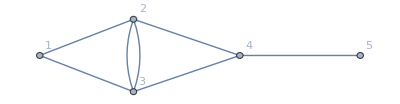

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->5,4<->2,2<->3,3<->1},VertexLabels->Automatic] (* Labelling vertices *)
```

```mathematica
el={1<->2,2<->3,3<->1};
```

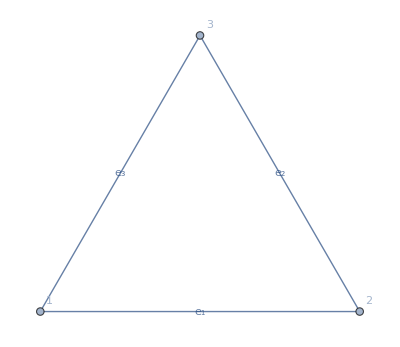

```mathematica
Graph[el,EdgeLabels->Table[el⟦i⟧->Subscript[e, i],{i,Length[el]}],VertexLabels->Automatic]  (* Lablelling edges Individually *)
```

We use graphs to capture useful relationships among entities, like in Social networks, the relationships between friends are captured in a graph. A graph is usually also called a network.

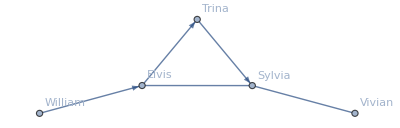

```mathematica
Graph[{"William" -> "Elvis","Elvis" <->"Sylvia","Elvis"-> "Trina","Trina"-> "Sylvia","Sylvia" <->"Vivian"},VertexLabels->"Name"]
```

A simple social network graph, the directed edges, the ones with an arrowhead are one way follow relationships like the one on Twitter and Instagram, for instance: William follows Elvis but Elvis does not follow William. Sylvia and Vivian both follow each other. 
We can model all sorts of situations with graphs, Your Google maps usually uses a graph to find the Shortest Path between two location.
There are other networks like Financial networks etc.

Uses of Graphs

Once we have a graph, we can ask several useful questions on the structures contained in the graph, this is how we use graphs as computational objects. e.g. 
1. Finding connected elements and paths
2. Finding the shortest path between elements
3. Breaking up or partitioning the graph into sets of connected elements.

```mathematica
cityConnections = {"Boston" <-> "Providence","Boston"<->"New York","Providence"<->"New York","New York"<->"Chicago","Chicago" <->"Denver","Chicago"<->"Phoenix","Denver"<->"Phoenix","Denver"<->"New York","Los Angeles"<->"Boston"};
```

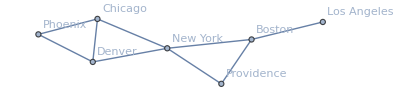

```mathematica
Graph[cityConnections,VertexLabels->"Name"]
```

We can do useful things like find the shortest path from one city to another

```mathematica
FindShortestPath[cityConnections,"Phoenix","Los Angeles"]
```

{Phoenix,Chicago,New York,Boston,Los Angeles}

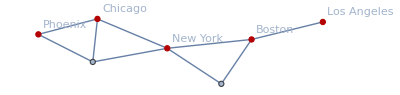

```mathematica
HighlightGraph[cityConnections,FindShortestPath[cityConnections,"Phoenix","Los Angeles"],VertexLabels->"Name"]
```

The example above might not be realistic, there are standard ways to find the shortest path between cities on a real map in WL, but we are using this toy example to demonstrate what we can do with graphs, this doesn’t scratch the surface of what is possible. Like I always say keep your documentation under your pillow. For those interested there is a whole section in the documentation dedicated to geographic computing, explore for more!